```mathematica
Quit[];
```

```mathematica
ScalarF0[g_,m_,s_]:=-g^2/(8 π^2)(√(4 m^2-s))/(√s)ArcTan[(√s)/(√(4 m^2-s))];
FermionF0[y_,m_,s_]:=y^2/(4 π^2)((4 m^2-s)^(3/2))/(√s)ArcTan[(√s)/(√(4 m^2-s))];
```

```mathematica
(8 π^2×M^3)/y^2 Refine[ComplexExpand[Re[D[FermionF0[y,m,s],s]/.{s->M^2}//Simplify]],Assumptions->M>2m>0]//Simplify
```

4 m^2 M-M^3+√(-4 m^2+M^2) (2 m^2+M^2) Log[-1+M/(√(-4 m^2+M^2))]-√(-4 m^2+M^2) (2 m^2+M^2) Log[1+M/(√(-4 m^2+M^2))]

```mathematica
ZvalScalar[g_,m_,M_]:=1/(1+g^2/(16 π^2×M^3)If[M>2m,-M+(4 m^2)/(√(M^2-4 m^2))ArcCoth[M/(√(M^2-4 m^2))],-M+(4 m^2)/(√(4 m^2-M^2))ArcTan[M/(√(4 m^2-M^2))]]);
ZvalFermion[y_,m_,M_]:=1/(1+y^2/(8 π^2×M^3)If[M>2m,-M(M^2-4 m^2)-(4 m^2+2 M^2)√(M^2-4 m^2)ArcCoth[M/(√(M^2-4 m^2))],M(4 m^2-M^2)-(4 m^2+2 M^2)√(4 m^2-M^2)ArcTan[M/(√(4 m^2-M^2))]]);
GammaScalar[g_,m_,M_]:=g^2/(16π×M^2)ZvalScalar[g,m,M]If[M>2m,√(M^2-4 m^2),0];
GammaFermion[y_,m_,M_]:=y^2/(8π×M^2)ZvalFermion[y,m,M]If[M>2m,(M^2-4 m^2)^(3/2),0];
```

```mathematica
GammaScalar[3500,400,1000]//N
GammaFermion[3.63,400,1000]//N
```

149.241

149.662

```mathematica
ZvalScalar[3500,400,1000]//N
ZvalFermion[3.63,400,1000]//N
```

1.02064

1.32155

```mathematica
ScalarRes[g_,m_,M_,GammaZero_,p_]:=Abs[p^2-M^2+ⅈ×M×GammaZero+ScalarF0[g,m,p^2]-Re[ScalarF0[g,m,M^2]]]^-2;
FermionRes[y_,m_,M_,GammaZero_,p_]:=Abs[p^2-M^2+ⅈ×M×GammaZero+FermionF0[y,m,p^2]-Re[FermionF0[y,m,M^2]]]^-2;
BW[Z_,M_,Gamma_,p_]:=Z^2 Abs[p^2-M^2+ⅈ×M×Gamma]^-2;
```

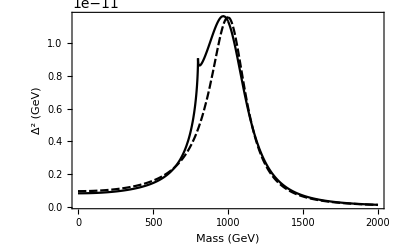

```mathematica
Plot[{ScalarRes[3500,400,1000,300-GammaScalar[3500,400,1000],p],BW[ZvalScalar[3500,400,1000],1000,300,p]},{p,0,2000},PlotRange->Full,MaxRecursion->15,PlotTheme->"Monochrome",LabelStyle->{FontFamily->"Times New Roman"},Axes->False,Frame->{{True,False},{True,False}},PlotRangePadding->0,FrameLabel->{{Style[StringForm["`` (``)",Abs[Δ]^2,Superscript[GeV,-4]],12],None},{Style["Mass (GeV)",12],None}}]
```

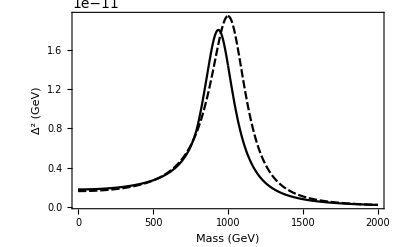

```mathematica
Plot[{FermionRes[3.63,400,1000,300-GammaFermion[3.63,400,1000],p],BW[ZvalFermion[3.63,400,1000],1000,300,p]},{p,0,2000},PlotRange->Full,MaxRecursion->15,PlotTheme->"Monochrome",LabelStyle->{FontFamily->"Times New Roman"},Axes->False,Frame->{{True,False},{True,False}},PlotRangePadding->0,FrameLabel->{{Style[StringForm["`` (``)",Abs[Δ]^2,Superscript[GeV,-4]],12],None},{Style["Mass (GeV)",12],None}}]
```